## 热学第五次作业

#### 2-2.

```mathematica
PDF[MaxwellDistribution[σ],x]
```

Piecewise[{{(ⅇ^(-x^2/(2 σ^2)) √(2/π) x^2)/σ^3, x>0}, {0, True}}]

```mathematica
Solve[D[(ⅇ^(-x^2/(2 σ^2)) √(2/π) x^2)/σ^3,x]==0,x]
```

{{x→0},{x→-√2 σ},{x→√2 σ}}

σ=√(kT/m)

故最概然速率为√((2kT)/m) .

(1).

```mathematica
Integrate[(ⅇ^(-x^2/(2 σ^2)) √(2/π) x^2)/σ^3,{x,0.99*√2 σ,1.01*√2 σ}]
```

0.0166032

故占约1 .66 %.

(2).

```mathematica
2*Integrate[PDF[NormalDistribution[0,σ],x],{x,0.99*√2 σ,1.01*√2 σ}](*考虑到正负方向都有故乘以2*)
```

0.00830243

故占约0.83%.

(3).

```mathematica
(2*Integrate[PDF[NormalDistribution[0,σ],x],{x,0.99*√2 σ,1.01*√2 σ}])^3
```

5.72289×10^-7

故占约 5.72×10^-5%.

(4).

在计算过程中我们也可以看到，这些百分数与温度并没有关系。

#### 2-6.

利用类似于惠更斯原理的思想，不同压强气体之间的扩散速率等价于各部分气体向真空扩散的速率的叠加。
而对于压强为p的气体，开个小孔即意味着本该在该区域反弹而留在容器的粒子离开容器。联系到最开始推导pV=νRT 时运用的方法，即
p A=(d(m v))/(d t)=2 v̄ dm/dt, 其中 v̄ 表示只沿着垂直于孔方向的平均速度。
dm/dt=(p A)/(2 v̄)

而

```mathematica
Integrate[x*PDF[NormalDistribution[0,√(kT/m)],x],{x,0,Infinity}]/Integrate[PDF[NormalDistribution[0,√(kT/m)],x],{x,0,Infinity}]
```

ConditionalExpression[(kT √(m/kT) √(2/π))/m,Re[m/kT]>0]

```mathematica
Simplify[(kT √(m/kT) √(2/π))/m]
```

(√(2/π))/(√(m/kT))

故 dm/dt= (p A)/(2 √((2k T)/(π m)))=1/2 √((π M^mol)/(2 R T))A p

二者叠加，即可得 1/2 √((π M^mol)/(2R T))A (p_1-p_2).

#### 2-9.

(1).

在一维时，v̄=(∫_0)^∞v f(v)dv /(∫_0)^∞ f(v)dv =1/2 v_0
二维时运用坐标变换，v̄=(∫_0)^∞v *2π v f(v)dv /(∫_0)^∞ 2π  v f(v)dv=2/3 v_0
三维时同理，v̄=(∫_0)^∞v*4π v^2 f(v)dv /(∫_0)^∞ 4π v^2 f(v)dv=3/4 v_0

(2).

在一维时， v_rms=√((∫_0)^∞v^2 f(v)dv /(∫_0)^∞ f(v)dv)=√(1/3)=0.577
二维时，v_rms=√((∫_0)^∞v^2*2π v f(v)dv /(∫_0)^∞ 2π  v f(v)dv)=√(1/2)=0.707
三维时，v_rms=√((∫_0)^∞v^2*4π v^2 f(v)dv /(∫_0)^∞ 4π  v^2 f(v)dv)=√(3/5)=0.775

#### 2-10.

p=(∫_0)^(√((2kT)/m))(ⅇ^(-(m v^2)/(2 kT)))/(√((2π k T)/m))dv = 1/(√π)(∫_0)^1 e^(-x^2)dx     (*x=v/(√((2kT)/m))*)
=1/2 Erf[1]
故分子数ΔN=p×N= 1/2 Erf[1].

#### 2-11.

p'=∫_v_0^∞ (ⅇ^(-(m v^2)/(2 kT)))/(√((2π k T)/m))ⅆv=1/(√π)∫_(v_0/v_max)^∞ ⅇ^(-x^2)ⅆx         (*x=v/(√((2kT)/m))*)
=1/2(Erf[x]-Erf[x_0]) /.x→∞
=1/2(1-Erf[x_0])

得证。

#### 2-12.

p=∫_0^v_0 (4π v^2 ⅇ^(-(m v^2)/(2 kT)))/((2π k T)/m )^(3/2)ⅆv=∫_0^x_0 4/(√π)x^2 e^(-x^2)ⅆx
=1/2(∫_0^x_0 4/(√π)e^(-x^2)ⅆx-∫_0^x_0 4/(√π)ⅆ(x e^(-x^2)))=Erf[x_0]-2/(√π)x_0 e^(-x^2)

得证。

#### 2-13.

p'=1-p=1-Erf[x_0]+2/(√π)x_0 e^(-x^2)
故分子数为N_0(1-Erf[x_0]+2/(√π)x_0 e^(-x^2)).

#### 9-2.

有Ω∝V^N.
Z=1/(N!h^(3N))∫e^-βU dΓ
	=1/(N!h^(3N))∫∫....∫e^(-β(1/2 mΣv^2))ΠdvΠdq
	=1/(N!h^(3N))*((√(2 π m))/(√β))^(3N)*V^N

```mathematica
Integrate[Exp[(-β*x^2)/(2m)],{x,-Infinity,Infinity}]
```

ConditionalExpression[(√(2 π))/(√(β/m)),Re[β/m]>0]

```mathematica
Clear[β];
D[-Log[V^n/(n!h^(3n))*((√(2 π))/(√(m β)))^(3n)],β]
```

(3 n)/(2 β)

故 U = 3/(2β)=3/2 n k_B T.

p=k_B(T((∂ln Z)/(∂V)))_(T,N)=(k_B T)/Ω((∂ Ω)/(∂ V))_(U,N)
=(k_B T)/V^N N V^(N-1)
= (N k_B T)/V
p V=N k_B T

F = - k_B T ln Z
S=k_B (ln Z - (β∂ ln Z)/(∂ β))

```mathematica
β=1/(Subscript[k, B]*T);
F=-Subscript[k, B]*T*Log[V^n/(n!h^(3n))*((√(2 π))/(√(m β)))^(3n)]
S=-D[F,T]
```

-T Log[(h^(-3 n) (2 π)^(3 n/2) V^n (m/(T k_B))^(-3 n/2))/(n!)] k_B

(3 n k_B)/2+Log[(h^(-3 n) (2 π)^(3 n/2) V^n (m/(T k_B))^(-3 n/2))/(n!)] k_B

又 n! ==(2Pi*n)(n/e)^n

```mathematica
D[Subscript[k, B]*T*Log[V^n/((2Pi*n)(n/e)^n h^(3n))*((√(2 π))/(√(m β)))^(3n)],T]
```

(3 n k_B)/2+Log[(h^(-3 n) (n/e)^-n (2 π)^(-1+(3 n)/2) V^n (m/(T k_B))^(-3 n/2))/n] k_B

由于n >> 1,
故上式简化为(3 n k_B)/2+Log[(h^(-3 n) (n/e)^-n (2 π)^((3 n)/2) (m/(T k_B))^(-3 n/2))/n] k_B
= 3/2 nk_B Log[T]+(5n k_B)/2+k_B Log[V^n/n^(n+1)]+Log[h^(-3 n)  (2 π)^((3 n)/2) (m/k_B)^(-3 n/2)] k_B
=3/2 nk_B Log[T]+(5n k_B)/2+n k_B Log[V/n]+Log[h^(-3 n)  (2 π)^((3 n)/2) (m/k_B)^(-3 n/2)] k_B

故S=3/2 nk_B Log[T]+(5n k_B)/2+n k_B Log[V/n]+Log[h^(-3 n)  (2 π)^((3 n)/2) (m/k_B)^(-3 n/2)] k_B

μ=(∂ G)/(∂ ν)=(∂ (F+p V))/(∂ ν)= (∂ (F + n k_B T))/(∂ ν)=k_B T Log[V^n/(n^n h^(3n))((√(2 π))/(√(m β)))^(3n)]
=N_A k T Log[N/V(h^2/(2π m k T))^(3/2)]      ,由于 (∂n)/(∂v)=N_A.

#### (7).

```mathematica
List1=Table[RandomReal[{0,1}],10000];
List2=Table[RandomInteger[{0,20}],10000];
N/@Mean/@{List1,List2}
```

{0.50121,9.9972}

平均值分别为0.50121，9.9972.

```mathematica
N/@Variance/@{List1,List2}
```

{0.0823048,36.4868}

方差分别为0.0823048, 36.4868.

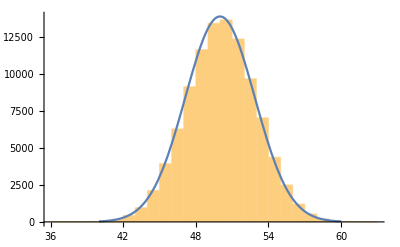

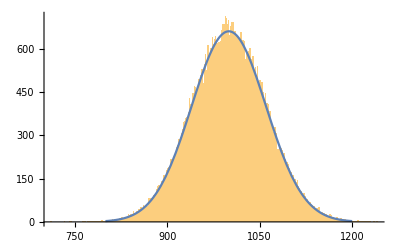

```mathematica
list1=Table[Total[RandomChoice[List1,100]],100000];
list2=Table[Total[RandomChoice[List2,100]],100000];
Show[Histogram[list1,{1}],Plot[100000*PDF[NormalDistribution[50,Sqrt[100*0.0823048]],x],{x,40,60}]]
Show[Histogram[list2,{1}],Plot[100000*PDF[NormalDistribution[1000,Sqrt[100*36.4768]],x],{x,800,1200}]]
```

中央极限定理得到验证。

#### (8).

(a).

```mathematica
List3=RandomVariate[NormalDistribution[],10000];
VectorList=Table[RandomVariate[NormalDistribution[],1000],3]//Transpose
```

{{0.58205,0.562968,-0.222653},{0.572809,-0.852412,1.49909},{-1.53834,-1.11009,-1.69866},{0.218684,-0.183332,0.27178},{-0.965352,0.23294,0.266897},{-0.69457,-0.952759,0.075457},{0.17726,1.31578,-1.27649},{-0.814702,-1.01805,0.011911},{0.0315077,-1.49511,0.185384},{-0.44667,0.763134,-2.1222},{-0.817403,1.7684,1.0082},{-0.421985,-0.731433,-0.387493},{1.40603,0.463836,-0.634921},{-1.16929,-0.151388,0.63095},{-1.12944,1.58621,0.220598},{0.906592,-1.55522,1.8283},{0.95641,-0.270253,0.0493576},{-0.677148,0.0577908,-0.651981},{1.29001,0.762495,0.0186747},{-0.16255,-0.705888,-0.60523},{-0.278935,0.357509,-0.0842753},{-0.54515,-1.07098,1.32724},{-0.430763,-3.11547,-0.879791},{0.754911,0.731678,-1.25447},{0.0876707,1.6595,1.97746},{-1.50403,0.699029,-0.185779},{-0.575514,1.45695,0.594029},{-0.799284,-1.22778,0.886876},{0.154159,1.11385,0.713322},{-1.93307,-0.937461,-0.693853},{-1.43045,-0.535337,0.460965},{-0.97821,-1.38038,-1.63631},{1.10462,0.68775,0.364323},{-0.468993,0.129725,-2.38767},{-0.515863,0.174871,0.151023},{2.16011,-1.43646,0.516969},{-0.182165,-0.908315,-0.922222},{-0.260184,-0.999998,-2.37864},{-0.529472,-0.894707,-0.825057},{0.0861951,-0.464607,0.182135},{0.345598,2.73257,-0.0949091},{0.481142,-0.980816,-0.326467},{-0.607361,1.14029,-2.08725},{-0.0138688,0.505416,-0.815545},{-0.863441,0.0566136,0.748852},{-0.418321,-0.0733005,-1.52054},{0.386518,0.9686,-0.0815823},{-0.265007,0.515197,0.83813},{0.437887,2.84922,-0.198491},{0.472483,-0.292572,0.0576141},{-0.644138,0.829114,0.42911},{-1.05326,1.91627,-0.377443},{0.794309,-0.695213,-0.547638},{0.695867,0.699165,-0.375958},{1.32394,-1.26993,0.793636},{-1.09945,-0.730591,0.151282},{-2.2808,3.05013,-1.3014},{0.633241,-0.295904,0.542645},{-0.786125,-0.71751,-0.328622},{0.457005,0.621038,-0.387669},{0.587513,-0.506445,-0.998505},{0.189801,-0.121482,-0.608566},{-0.613884,-0.166402,-0.00459209},{-0.91256,-0.0292585,-0.886328},{-0.461165,-0.932358,-0.797351},{0.383,-1.65949,2.12891},{0.267182,0.147504,-2.09783},{-1.23683,1.13142,-0.68799},{0.86836,-1.67859,-0.0749206},{-0.93226,-0.709305,0.681045},{-1.90397,-0.288777,-0.0694895},{-1.17453,0.511802,-0.941117},{-0.139519,0.795167,-0.729691},{-0.199396,1.13121,-0.824101},{0.244228,0.0778592,1.73381},{0.907441,-1.89969,0.640846},{1.58346,-2.34892,-0.31397},{-1.13518,0.698029,-1.62669},{-1.69756,1.15223,0.036151},{-2.07243,-0.803937,-1.3291},{-0.0494503,-0.517016,-0.748803},{0.200591,2.02691,-0.479192},{-0.23828,-1.16861,-0.00514482},{0.230171,-0.664395,2.18153},{-0.453835,0.722019,-0.708626},{0.502729,-3.13327,-0.908381},{0.752945,-0.0109902,0.427431},{-1.22004,-0.742479,-0.413882},{1.4363,-0.54574,0.390978},{0.104118,-1.8041,-0.0724809},{-1.48167,1.63055,-0.333683},{-0.506468,-0.00486138,1.34511},{-1.37218,0.251615,0.239655},{-0.674863,-0.88422,-0.430502},{0.242756,-1.63016,-0.725803},{-0.690809,0.537114,2.24234},{-0.839441,1.15218,-1.92696},{0.15485,-1.612,0.901934},{-0.344836,-2.39974,1.46858},{2.83617,0.2851,0.303573},{-0.939772,0.118603,0.834532},{-0.0490587,0.817076,0.402848},{-0.684254,0.25163,0.82356},{-0.965412,0.0280766,-0.383966},{-1.10295,0.322952,-0.361079},{0.522965,2.17296,0.930587},{-1.32779,-0.522964,-0.933863},{1.14533,-0.174751,-0.341314},{-0.626428,-2.11721,-1.29016},{-1.35816,0.122269,0.877186},{0.533135,-1.38413,1.41124},{-0.474486,1.50717,-0.894022},{1.31494,-1.8935,1.27176},{-0.325877,0.182555,-0.982839},{2.02092,0.763772,-0.864484},{-0.262763,0.333764,1.07149},{-0.575479,-0.810466,-0.588296},{-0.646,-0.475728,0.26786},{2.78987,-0.267324,-0.757176},{-1.68445,2.1034,1.16482},{0.553648,-0.479097,0.173568},{-1.24739,0.519804,-0.00648271},{1.46421,-0.0952686,0.947705},{1.68548,0.12765,-0.127652},{-1.10157,0.227057,-0.403651},{-1.45662,-0.873454,1.79897},{1.17968,-0.71903,0.434866},{-1.45528,-0.21582,0.43054},{0.709593,-0.310965,-0.665506},{1.71592,-1.09978,-0.520465},{1.13489,0.178838,-0.988252},{-0.88831,-0.265507,0.408818},{-1.49216,-0.200749,0.0595394},{1.12405,-0.0297734,2.24472},{-0.259979,0.269797,-0.588327},{0.206876,1.85918,-1.68744},{0.721038,-1.58381,-0.0642581},{-0.135234,0.428974,0.00379402},{-1.193,-1.04827,-0.737438},{-1.63158,-1.74022,0.330526},{0.348645,-0.93302,0.497093},{-1.04182,-2.066,0.42366},{-0.633482,-0.444374,2.31176},{0.992316,0.276407,0.698231},{-0.0849102,-1.35274,-2.18611},{-1.9225,0.355113,-0.23714},{1.07215,-0.751413,-1.06257},{-0.369512,-1.69134,-0.0926865},{0.179305,-0.96776,1.96148},{-0.158487,-0.615726,-0.65581},{-0.646801,-0.712139,-0.719552},{-2.12945,0.358886,-0.615492},{1.18288,-0.626427,-0.872244},{-1.55883,-0.434406,-0.974314},{0.840979,1.37323,0.831808},{-0.631507,-1.13451,-0.465131},{0.297697,-0.425771,0.708007},{1.25349,-0.631776,1.40089},{-0.533755,-0.207008,-0.529991},{-0.337485,-0.619604,-0.330474},{1.707,1.94214,-0.208021},{-1.11699,-1.36192,1.1832},{0.562588,-1.52215,-2.03018},{-1.33103,-0.563599,1.26755},{-0.338225,-1.27155,0.378795},{0.423495,-0.47593,-0.182216},{-1.31273,0.260338,-0.594634},{1.13567,-1.5527,0.89168},{-1.34982,-0.0828278,0.27538},{0.00166135,-1.34303,-0.123773},{-0.36613,1.96529,1.59708},{1.35431,-0.218539,-0.451196},{-1.05097,0.506504,0.0395883},{0.927011,0.00894854,-0.603685},{-0.305965,0.715078,-0.213581},{-0.25909,0.86378,-2.20051},{-0.0293286,-1.29828,-0.454541},{0.854888,0.890434,-0.849961},{0.274761,0.274044,0.963417},{0.0727412,-0.744914,-0.432418},{0.249128,-0.47925,0.116153},{-1.57085,1.0516,0.735615},{0.124091,-0.732777,-0.0134778},{-0.626936,0.697243,1.09953},{1.31179,0.246318,0.380612},{2.18267,2.46613,-0.88737},{0.878162,-1.44987,-1.60365},{-0.862048,-0.515499,0.775238},{-0.686837,-1.01951,-1.50909},{0.444118,0.594683,-0.540978},{-2.10425,-0.415602,0.820666},{-0.550098,-1.57442,-0.177701},{0.189508,-0.639094,0.334821},{0.0664363,1.00956,-0.788095},{0.89321,1.69367,1.45894},{-1.09504,1.49205,-1.45995},{0.233572,2.16059,-0.870524},{-1.37319,-0.0182116,-1.55281},{-0.249628,0.0297454,1.0891},{-0.106016,1.59307,1.20081},{-0.176251,0.781793,-0.385832},{0.147179,1.07529,-0.465496},{2.43566,-0.342552,1.36826},{0.597139,-1.38202,-0.481316},{0.962288,1.52595,0.695187},{-0.358655,0.603318,0.382853},{1.3381,-0.336005,0.56475},{0.286935,-0.703467,0.534866},{-0.314548,0.591819,-0.0719518},{0.0509342,-0.400523,0.501918},{1.20637,-0.734638,0.389379},{0.300786,-0.200534,0.582248},{0.433102,-0.0439433,0.783135},{0.0391341,0.604688,-1.87084},{1.01866,-0.0515861,-0.357379},{1.05738,2.30097,-0.520906},{2.22777,-1.04576,0.94657},{0.709882,1.29801,-1.18659},{0.790245,0.759763,1.32842},{-1.72385,1.33885,1.14086},{-1.38127,-1.41164,-0.811499},{0.301362,0.569467,0.402403},{-0.787752,-0.323867,-1.12876},{-0.681419,1.65895,0.753168},{0.70749,0.370895,-0.714266},{-0.55942,0.0705331,0.861066},{-0.989764,0.951157,1.50614},{-1.17635,-0.0377198,-0.0611008},{-0.436426,0.170824,0.631722},{1.95129,0.466222,1.89147},{2.03299,0.703458,-0.408973},{-2.27756,1.50502,0.478456},{1.39531,1.45285,-0.939865},{0.412577,0.0158144,0.343485},{0.157258,-0.260406,-0.875092},{-0.389513,-0.177601,-0.457001},{-0.244914,0.777366,1.50373},{1.09836,-1.2415,-1.24032},{-0.378958,0.47352,0.226515},{0.391828,-0.875679,0.274026},{-0.991495,1.42216,-0.248186},{1.30097,0.766898,0.877361},{-1.55051,-0.492564,-0.973507},{1.84593,0.318814,1.50975},{-1.17972,0.410292,0.678733},{1.82313,0.11926,0.58394},{-2.50132,0.741102,-0.237703},{-0.0867905,1.24105,-0.398364},{-1.76294,1.50766,0.382316},{-1.12219,-1.31367,0.688049},{0.0193817,-0.671116,0.447899},{2.51125,-1.51647,0.154094},{-1.73598,-1.62163,0.244167},{1.1012,-0.89444,-0.318207},{-0.115596,1.0213,-0.380087},{1.60881,0.66333,-0.297286},{1.3724,1.52156,-0.741295},{-0.115579,1.05155,0.236782},{-0.213722,2.2877,0.119741},{-1.03364,-0.671452,-1.19144},{0.864424,0.649774,-0.615216},{-0.959798,1.95914,1.46324},{0.569017,1.46398,-0.520261},{0.480847,-2.45734,0.816179},{1.49222,-1.02207,-1.66974},{0.172396,-0.488121,-2.76111},{-0.780659,1.33869,-1.03658},{-1.60498,-0.166907,-1.67372},{1.94682,-1.13534,-2.30344},{0.146713,0.392075,-0.0873476},{0.766675,0.954891,-0.440948},{-3.00497,-0.347066,2.26041},{1.00324,1.46272,1.12496},{1.23975,1.57415,1.14694},{-0.795077,-0.871506,1.21732},{-0.137787,-0.561814,-1.52092},{0.127187,-0.520598,0.069572},{0.301347,-1.37297,-1.49005},{-0.24598,-0.767997,2.42256},{0.493862,0.0237442,-0.0749116},{0.756324,0.659941,0.586582},{1.64955,0.355384,0.391534},{0.811066,-0.014935,-0.985556},{0.60281,-1.55109,0.571264},{0.189011,-0.658767,-0.415733},{0.279054,1.41768,-0.861725},{-0.350173,-0.395284,0.743415},{0.211535,-0.453011,1.29076},{1.1578,1.4639,-0.310698},{0.791837,-0.718298,0.435262},{0.379267,-0.299245,-0.0564162},{0.119808,-1.14745,0.16571},{-0.430939,-0.0485763,-1.68546},{-0.457315,2.76878,0.573122},{-1.22572,-0.957728,0.421604},{-0.765679,0.93034,0.236428},{0.637805,0.571775,-0.43166},{0.678354,-0.27034,1.0413},{1.47474,1.29477,0.553927},{-1.01267,-0.227823,-0.265002},{-1.34745,0.117468,0.483013},{0.676388,-0.862571,0.943274},{1.97367,1.1895,1.07539},{-0.734758,-0.106387,-0.876137},{2.08736,-0.854419,0.852772},{1.52613,-0.0957685,0.743799},{-0.837358,0.659591,-0.702176},{0.0212305,0.795036,0.0334897},{-1.59479,0.222798,-0.267249},{-1.73449,0.545027,0.399492},{1.7043,0.0910826,1.89471},{2.1635,-0.190806,-1.18988},{0.217641,0.451331,1.47011},{2.5386,1.03701,-0.95458},{1.30356,0.69605,0.548079},{0.901525,-1.46075,1.44321},{-2.00534,-1.13948,1.36268},{0.426764,-0.310006,-0.39985},{0.184584,1.08604,-0.156196},{1.23276,-0.858704,0.114437},{1.8667,-0.854277,-0.299526},{-0.913744,-0.0671694,0.186131},{0.657079,1.13523,-1.21745},{-0.796955,-1.00455,-0.0392428},{-0.443824,-0.111208,-0.964519},{-0.775393,-0.912478,-1.1878},{-1.32969,0.422027,1.9466},{0.608599,1.54635,0.791276},{-0.730666,-0.421647,-1.72565},{-0.230991,-0.899497,-2.14736},{0.522972,-1.04539,0.97844},{0.463803,1.28587,-0.335126},{-0.110186,-1.6728,-0.142797},{-1.52727,-0.294814,0.156536},{1.85104,0.351929,-0.401142},{-0.35926,0.48477,1.32982},{-1.88539,1.78577,-0.924105},{-0.19832,-0.648295,0.195591},{0.294167,1.89471,0.484969},{0.669938,-0.747292,-1.2865},{-0.348,-0.462874,0.883821},{-0.491491,-1.18777,-1.15219},{-0.191665,1.65226,0.526609},{1.09156,-1.50645,-0.319367},{-0.0497978,-0.948391,-0.204917},{0.0493968,1.7223,1.93995},{-0.0017661,0.0770355,-0.880793},{0.457299,1.47803,-0.767409},{-0.429089,-0.154013,-0.910727},{0.693902,1.02187,-1.2858},{-0.323185,0.572467,0.0590663},{-0.707532,-0.528741,1.26004},{0.825156,1.1279,0.17812},{0.126153,-1.64856,-0.648171},{1.5642,0.967881,-0.795338},{-0.615396,-0.0940612,-0.921106},{1.46606,0.252339,-0.0122862},{1.40925,-2.18328,0.379056},{2.0618,-0.623659,-0.85239},{-0.737992,0.428362,-0.152793},{1.33464,-0.426647,0.834872},{-1.0069,-1.44604,1.40323},{-0.314804,0.136443,0.631322},{-0.0188006,1.04827,-0.564797},{-0.268696,-0.238614,0.55222},{-0.626592,-0.263085,0.529279},{-0.788597,0.0273676,0.684494},{0.963901,-0.591061,-0.827906},{-0.630222,0.514548,-0.444305},{-0.363741,0.440797,0.120016},{-0.472828,-0.465279,-0.0356472},{1.78433,-0.113183,1.55758},{0.635925,1.28486,-0.665226},{1.45639,0.272498,2.37354},{-0.413639,-0.102615,1.39874},{0.402496,0.547878,-0.168439},{-0.996776,1.21518,-1.91402},{0.326092,-0.411081,0.414234},{0.39207,1.85806,0.430311},{0.554572,-0.368264,0.162016},{0.206156,-0.531457,1.84304},{0.356306,1.8175,-1.6046},{-0.448174,1.05531,-1.12557},{0.377135,-0.697901,0.034103},{0.723201,-0.712662,1.9042},{0.298893,0.419495,1.07005},{0.347612,-0.532108,-1.21329},{-0.128495,0.792691,1.0181},{-0.998685,-0.223098,-0.890327},{-0.238412,0.283072,-2.78479},{0.148132,-0.521277,0.0135752},{1.64788,1.21413,0.94308},{0.377411,-1.18746,2.12897},{1.52643,-0.43107,-2.19975},{1.4558,-0.853643,0.419613},{0.854446,0.168804,1.85141},{2.00613,-0.524875,0.419348},{0.596073,0.61415,-1.27255},{0.90493,-0.789794,1.69897},{-0.0106262,0.000515428,-0.420976},{-0.0686263,-0.917758,-1.10194},{-0.536007,0.531762,-0.205589},{-0.571347,-0.749678,1.18664},{-1.07613,-0.146375,-0.714837},{-0.950472,1.64086,0.825299},{-0.916108,-0.946599,1.44704},{-0.779242,0.78727,1.58185},{0.642888,-0.156181,-0.588921},{-0.139251,0.405296,0.790798},{-1.16185,-0.203919,-1.24303},{-1.4024,1.07434,0.698935},{0.394401,0.843835,1.23869},{2.15911,0.356973,-0.466112},{-1.16241,0.498443,1.04064},{1.91952,-2.00075,2.52668},{0.257777,0.754391,0.00509529},{-1.4447,-1.42165,-0.778146},{1.14388,-0.623749,-0.377142},{-1.10688,0.782422,1.20006},{0.63357,0.579592,-0.295149},{0.257136,0.920266,-0.195702},{1.7949,-0.307855,-0.0976439},{-0.230554,-0.980923,0.547744},{1.80798,1.60595,0.615841},{-0.945079,0.122587,2.70624},{0.801854,-0.972775,0.781958},{-0.358133,1.25281,1.26578},{-0.120518,0.589632,0.519081},{2.51052,-1.07244,0.0659541},{1.46921,-1.02938,-0.135553},{-1.24783,-1.25428,1.50592},{0.604567,-0.533339,-0.693273},{1.96567,-0.87625,0.962554},{-1.55334,1.65345,-0.50992},{-2.17883,-1.25507,0.193258},{-0.270253,0.527126,-0.736158},{-0.770988,-0.622608,-1.44337},{-0.68406,-1.03543,1.59976},{0.930986,-0.106219,1.16734},{-0.310762,1.27245,0.891014},{0.430059,-0.373934,0.94187},{-0.749735,2.10436,1.31602},{1.90552,0.127507,0.909709},{0.0701378,-1.02177,-0.482544},{-0.072986,0.908077,-0.463517},{0.0372693,-0.667949,0.758227},{-1.84582,0.495798,-0.204465},{-0.733099,-0.978026,1.15364},{-0.630429,-1.65883,0.281799},{-0.102209,1.63036,0.29076},{1.51123,1.16749,1.43702},{-0.602921,-0.503422,0.052801},{1.01223,-0.179947,-0.221608},{-0.157631,0.607125,0.0288854},{1.07577,1.3067,-1.31103},{0.272484,-0.0161544,-0.843621},{0.34958,0.787766,0.854654},{-0.357551,-0.710276,1.40185},{-1.35536,0.137357,0.275592},{1.05915,0.664411,-1.79272},{1.39588,0.563993,-0.282902},{-2.20849,-0.380572,2.02387},{-0.752956,-1.15977,-0.708766},{-1.23677,2.40714,-0.0464649},{1.48903,-0.870591,-2.2681},{0.800697,-1.1108,-1.14839},{0.172672,-0.654184,0.792319},{-0.539758,-0.196564,1.27969},{-1.27857,0.0263879,0.926303},{-0.553213,-0.905819,0.706456},{-0.855091,0.404157,0.950012},{-0.738826,1.06914,-0.939057},{0.477877,0.716021,0.678766},{1.41208,0.776525,-1.50048},{-0.90544,-0.502236,-1.66308},{-1.37573,1.48249,1.3956},{-0.303876,0.809325,0.0834163},{0.0536375,-1.23989,-0.851817},{-1.69073,-0.184835,1.1693},{-0.0976476,0.855038,-1.30922},{0.127552,-2.87515,0.707333},{0.631442,-0.267482,-0.79477},{-1.27976,-0.864073,0.169024},{-0.794072,-0.826101,1.19655},{1.87259,-0.549259,0.269023},{1.39383,1.64075,-0.705875},{-0.408264,1.62208,-1.74728},{-0.319456,-1.29023,0.610474},{-0.841279,1.5073,-0.46587},{1.31388,-1.2223,0.402485},{1.86839,-1.83773,0.813051},{-0.835887,-0.0394035,0.401076},{-1.14756,-1.47925,-1.33149},{-0.562638,0.811018,0.197427},{0.517509,-1.46928,-0.401782},{0.122815,-0.0731104,-0.418754},{-0.6361,-2.534,0.261654},{0.189249,0.427008,2.74497},{-1.06894,1.59431,0.109423},{-0.616723,-0.195791,0.306731},{-0.397654,0.472616,-1.09262},{1.23536,0.451177,0.225498},{1.10074,-1.14561,-0.0860516},{0.0874442,-1.2233,0.585692},{1.11972,-0.954345,3.00426},{-0.249106,-2.09103,0.353663},{0.0965498,-1.93668,-0.435676},{-0.211913,0.693298,0.989939},{-1.01987,0.62013,0.110576},{-0.173215,-0.033647,-1.9419},{0.151386,-1.35217,0.215564},{-0.078293,-0.968403,-1.04756},{-0.0104563,0.24971,0.204517},{0.622116,-0.0627227,-0.0211425},{0.58859,-1.00687,0.753626},{-0.160689,-2.41995,-1.32659},{-2.48581,-0.020221,0.319349},{0.418976,-1.07,0.48346},{0.697775,-0.52804,0.654945},{-0.574276,-0.461678,-0.88455},{-0.754995,1.22195,0.377943},{2.07839,-1.63314,-0.293823},{0.983409,0.053497,0.651562},{-0.0468979,1.08906,0.827112},{0.124553,0.0537056,2.24792},{-0.0629873,0.230245,0.924058},{1.70688,-0.526191,0.65486},{-0.179009,-0.388409,0.747723},{2.1577,0.809112,1.69863},{-0.903948,1.96389,1.13425},{-1.52519,-1.76891,-2.95821},{1.9474,-1.05083,-0.0526273},{0.639956,-0.0495102,0.518979},{-0.873451,1.53046,0.401838},{-0.842526,0.593085,-0.121734},{0.360047,0.0722623,-0.865298},{-1.14588,-0.344945,1.07818},{0.901815,-0.627731,-0.157435},{0.326889,2.15877,0.36712},{-0.773976,0.437677,0.743628},{0.346081,-0.489918,1.42692},{0.30543,-0.101382,0.623507},{2.35268,-0.968259,1.95296},{-0.179826,-0.60649,1.07314},{1.25046,0.612345,0.9555},{0.0569987,0.0275899,1.13525},{-0.652643,0.00585887,0.390977},{0.7454,1.13679,-0.629349},{1.77826,1.23608,0.513727},{-1.26801,0.912161,-0.993298},{-0.415935,1.3409,0.363416},{1.09067,-0.596078,1.82241},{0.750452,-1.12634,-0.00976742},{0.304295,0.0704429,0.487434},{0.140383,0.010128,-1.99689},{0.460066,0.626041,-1.76763},{0.810182,-0.235064,-0.435998},{-0.558783,-0.239097,-0.362611},{0.0425744,0.996149,0.750226},{0.282842,0.688173,0.77506},{0.426802,-0.641094,0.15872},{1.08447,0.769418,-0.0186463},{-0.0901392,0.759423,0.00809125},{-0.610993,-0.895889,0.60589},{-1.01875,-0.585707,0.469907},{0.0655226,0.35206,2.07634},{1.17111,0.945293,0.465451},{-0.918277,-0.166725,0.666774},{1.94932,0.506551,1.39839},{0.948756,-1.12631,0.105033},{-0.534052,1.23369,0.624971},{1.58349,1.63032,-0.154945},{-1.68013,-0.747413,0.479305},{-0.73251,0.208877,0.319387},{0.844729,-0.4236,-0.90266},{1.10934,-0.322825,1.06448},{0.28115,0.492354,0.878191},{0.306346,0.521624,1.47421},{1.13126,0.249075,-2.43918},{-0.985734,0.161311,-1.6026},{0.350314,1.39831,-0.209013},{-1.08099,0.87111,1.00151},{-1.72651,-2.05602,0.643843},{-1.67979,0.261697,-1.88599},{0.217815,0.297215,0.542536},{1.34307,1.03738,-1.39811},{0.211874,2.13778,0.714623},{-0.910169,1.25301,1.33488},{-2.00068,0.880057,-0.815093},{1.48877,1.42268,0.68151},{0.877937,-1.53442,0.553233},{-1.37937,1.12547,-0.385527},{0.249927,0.986234,0.375989},{0.467666,0.129866,-0.974665},{-0.836032,-1.47483,0.555795},{-0.106579,-0.58159,-0.528085},{1.70669,1.26213,0.195736},{-0.335177,-0.820723,0.610507},{-0.100802,-0.0795521,0.167973},{-1.34857,-0.270497,1.03543},{-0.0965675,0.831433,-0.30901},{0.56274,-0.860341,-0.562843},{-0.53905,1.44527,0.695235},{0.649754,0.541411,0.03943},{0.806756,-1.17128,1.02181},{0.59317,0.633124,1.16024},{1.23793,-0.186475,0.477053},{-0.617142,2.6368,0.0403931},{1.58957,-1.17536,0.189997},{-1.65985,0.84071,-0.256625},{-2.06027,0.401675,-0.692831},{0.967093,-1.15683,0.126906},{0.499452,1.00652,0.188904},{1.16341,-0.950447,0.167374},{-1.5793,-0.723322,-2.09414},{0.280477,0.793573,-2.63395},{-2.87783,-0.0535228,-0.525912},{-1.68908,1.6949,0.167815},{0.316987,-0.234713,0.47537},{-0.382254,0.362998,0.947201},{-1.80454,0.15395,0.351588},{-1.01215,-0.220588,0.0833817},{-0.197722,-0.246807,-1.87202},{0.729924,-0.529767,2.41688},{-1.08735,-0.00933117,1.0705},{-0.754241,0.135151,0.954869},{0.401844,0.364296,1.57154},{1.03645,-0.50622,-0.248967},{-0.831647,0.203215,1.14846},{-0.807227,-3.35539,0.0816917},{0.175298,-0.769509,-1.23568},{-0.608903,0.348519,-1.43831},{0.0925572,-1.1647,0.20092},{-0.123169,-0.861188,-0.858873},{0.721071,0.0805324,1.35285},{-0.626008,-1.21472,-0.331257},{1.80473,0.504138,-1.02605},{0.386727,-0.516855,0.350437},{0.196235,1.24705,0.362626},{-0.378895,-0.419134,0.875585},{-1.93243,-0.384761,-0.169896},{0.0945567,-2.73964,-0.325767},{1.2158,0.358315,-0.392774},{0.125325,-0.0149657,0.589041},{0.984942,-0.765419,0.635463},{-0.254493,-0.820418,0.816703},{-0.096522,-0.453192,-0.195613},{0.682051,1.85084,0.0140579},{-0.708723,-0.231748,0.234603},{-0.0477234,-1.24502,-0.253307},{-0.447111,0.382219,-1.89665},{0.591733,1.10028,-0.471117},{-1.22305,0.144949,-0.26496},{1.65131,0.0473236,-0.117261},{1.08974,-0.151524,-1.36681},{-1.11613,-1.11995,1.47482},{1.64539,0.474871,0.306677},{-0.894646,-2.3673,-1.28279},{1.056,-0.681036,-0.252524},{-0.47423,0.0834927,1.44381},{0.888209,0.422598,-0.635894},{0.739001,0.395203,-1.19396},{1.35345,-1.41508,-0.0294448},{-1.06951,-1.45062,-0.657886},{-2.0138,-0.889781,-2.44538},{-2.89534,1.03007,1.44154},{-0.566282,0.884545,0.561355},{0.575797,0.0197992,0.357535},{-0.0493837,-1.14779,0.0150181},{-0.648469,-0.137798,-0.517613},{0.372432,-0.497017,0.806677},{-0.824421,-0.179264,-0.67486},{-1.67176,-0.912111,-0.786297},{0.165503,-1.55475,-0.393148},{-0.755659,-1.96908,0.333983},{-3.02776,0.468679,-0.962473},{0.0241719,0.158295,1.03383},{1.29796,-0.665115,-0.237066},{-0.336061,-0.478529,0.596596},{0.0502408,0.0406809,0.690098},{0.145003,0.0892263,2.62806},{-1.68807,0.137885,-0.530588},{0.418811,-0.911155,0.516652},{-0.962467,0.140459,-0.460983},{-0.393908,0.414925,0.847774},{1.20132,1.49626,-0.136254},{0.420281,-0.337348,0.48792},{1.25049,-0.110952,0.802865},{-0.928586,-1.05191,-0.681842},{1.73478,-0.883619,1.10136},{-1.66983,0.829274,-0.037085},{-0.385527,-1.92648,-1.65542},{-1.64471,0.842995,1.7683},{-2.29161,1.1723,-1.02209},{1.06817,-0.46775,-1.47037},{-0.129522,0.975851,-1.38004},{-0.125706,-0.74706,1.53571},{0.0719847,-1.67557,0.564262},{-0.061531,0.105972,0.0558073},{0.894364,0.593817,0.0147455},{-0.282882,-0.993573,-0.153359},{-1.19554,-0.000398673,-0.453674},{-0.311878,0.974287,-1.41314},{1.96579,0.957071,0.506365},{-1.17968,-0.7668,-0.369177},{-0.261989,0.47015,-0.675626},{2.80689,-0.189211,-0.715079},{0.781077,-0.00820491,-0.214572},{-0.139899,-0.345754,-0.148711},{-1.04517,0.446302,-0.178688},{0.271363,1.46847,1.2486},{-0.899217,-0.0299317,0.285546},{0.352402,2.08772,-0.538231},{0.432698,0.0279801,-2.04945},{0.0762449,0.761326,0.261076},{-0.754977,-2.0376,-0.39345},{-1.74176,-1.10552,-0.242462},{-0.933205,0.166804,-1.03766},{-1.46109,0.203888,2.2476},{-1.42618,-0.892666,1.8056},{-0.721734,0.581994,-0.926157},{1.41099,0.290393,-0.828568},{-1.59979,2.02586,-1.0085},{-0.924059,1.20968,0.684547},{-0.399233,-0.0226648,0.235806},{0.397041,-0.190278,1.48363},{0.502978,-0.600173,0.326697},{0.973025,0.26298,-0.805804},{-0.239569,1.40404,-0.634415},{1.01007,1.39208,0.234848},{-0.259329,2.18716,-0.772789},{-1.49251,0.898248,2.19176},{0.822914,0.0242399,1.97692},{-1.13452,0.76564,-0.719103},{-1.66068,1.44303,0.289987},{0.580888,-0.361314,-1.14162},{-1.91906,-0.170616,2.12682},{-0.429366,-1.03141,-1.80343},{1.09212,-1.15119,1.16845},{-0.451484,1.76843,-1.86665},{-0.390948,0.700277,0.519919},{-0.695527,1.30532,1.21868},{0.0821843,-1.66985,-0.425683},{-1.23744,1.42711,-0.892859},{2.29423,0.16932,1.90872},{-1.53911,-1.49024,-1.17957},{0.507145,0.0682615,0.318876},{0.933157,-0.638801,-0.0941393},{1.19134,-1.02234,-0.866988},{-0.338496,0.75376,1.20674},{-0.757404,-1.87167,-0.131734},{-0.0693113,1.25045,-1.08538},{0.72258,-1.16899,0.571884},{0.689137,0.658338,-1.72049},{0.316401,0.361413,-0.857708},{0.408103,-0.922678,1.04793},{0.260438,-0.2214,0.217406},{0.25745,-0.32221,0.136919},{-0.664783,-1.24631,2.12476},{0.61193,1.26881,0.011613},{-0.968727,1.52081,0.677517},{0.235654,-2.82115,0.267498},{1.7017,0.284673,2.81013},{0.839445,0.675863,-0.172201},{-0.014531,0.305961,0.385637},{0.363645,-0.364344,-0.26287},{-0.70076,-1.30366,2.73999},{0.0230579,-1.25587,0.868148},{-1.77116,-0.61491,-1.18771},{-1.6423,1.48633,-0.759613},{-0.71185,1.29265,-0.648686},{0.520041,0.0404495,-1.80918},{0.0108406,-0.346719,-1.25369},{-3.1897,-0.121461,0.183438},{-0.186144,-1.24345,-0.507406},{-0.0493427,1.16827,1.93617},{-0.5734,-1.38831,0.363532},{-2.25342,-0.201218,0.101528},{-1.39942,2.88543,-0.704054},{-0.253505,-1.86222,-0.0779526},{0.60811,1.00228,-0.00372896},{0.126757,-0.847513,0.603505},{-1.12776,0.906455,0.462657},{0.12723,-0.17588,-1.05633},{0.341947,-0.312418,0.030448},{0.119863,-0.205873,1.29296},{0.215272,-0.0408997,-0.550889},{-0.934202,-0.52388,0.466838},{-0.0609346,0.881495,-1.94957},{1.43434,-1.73861,-0.492138},{-2.21221,-0.511518,-1.46315},{-0.670246,0.720449,-0.3026},{-0.775707,-1.30261,-1.08178},{-0.515318,0.70765,-0.457303},{-0.354409,0.260942,0.455018},{1.42508,0.128459,-0.46614},{1.67899,1.24006,0.476078},{-0.212246,-1.52905,0.505036},{-0.696813,1.59052,-0.546517},{0.89642,-1.20264,0.340921},{0.823497,0.661438,0.0312871},{0.944291,0.162275,0.824523},{-0.75173,-1.67408,0.452126},{-0.507268,-0.206612,0.245268},{-0.565075,0.28687,-0.425209},{-1.04346,0.168959,-0.502378},{1.26455,-0.0309171,-0.802603},{-0.151349,1.94376,0.517654},{0.0136105,0.121573,-0.633099},{-0.931669,0.979883,1.02827},{0.96003,-1.23979,1.94376},{0.889342,1.08654,0.680958},{-0.452634,-2.49769,-0.701591},{-0.552338,-0.543802,0.377543},{-0.236366,-0.813061,-1.1047},{-0.421444,-1.17203,0.702498},{0.810048,-0.193686,0.241002},{-0.67536,1.37544,-1.26503},{0.763997,1.79621,-0.664441},{-1.28686,-1.89305,-0.435737},{-1.07063,0.77438,1.39971},{1.16489,-2.0665,-0.0939802},{-0.8839,-0.286016,-0.640808},{0.202435,-0.413529,-1.00043},{-0.180351,-0.736931,1.25234},{0.322938,1.13942,0.767722},{0.218311,0.0468584,0.358049},{-1.53956,1.25467,-0.49441},{0.176984,-1.26352,0.827491},{0.639199,3.33859,0.632223},{-0.968794,0.0811943,-0.456682},{-1.47565,-0.806076,-0.398672},{0.537785,-1.04954,1.2867},{-1.30431,-0.266023,0.809204},{0.559526,0.673134,-0.358428},{-1.06145,0.583905,0.32691},{-0.512204,-0.787835,1.2133},{-1.58233,0.161183,-2.11318},{-0.268221,0.301249,-0.368124},{-1.33121,-2.05064,2.26699},{-0.457475,0.302621,0.42314},{-1.21889,-0.87471,0.181057},{-0.986317,0.153334,1.18056},{0.677118,0.0823348,1.192},{-1.76176,-0.714962,1.08852},{0.991259,-1.32222,0.345365},{0.0863109,-0.347813,-0.39171},{-2.65094,1.03019,-1.16512},{-0.591086,-1.18467,1.31494},{0.0210332,0.343008,0.691181},{1.26908,-1.97192,0.996732},{0.436498,1.39945,-0.0465436},{-0.873404,0.626187,0.123074},{0.866568,-0.968889,-0.841137},{-1.07401,1.79039,0.556086},{0.469415,2.58956,1.13398},{-1.01856,-0.23829,0.034759},{0.585972,0.506764,-0.14487},{-0.501061,0.848254,0.477372},{2.12585,-1.03307,0.121742},{0.734011,0.877414,-0.679649},{0.613586,-1.67693,-0.788954},{1.57265,-0.554589,-0.323235},{1.13314,-0.0742637,-0.58018},{-0.692768,-0.415777,0.311861},{0.426486,0.585127,-3.07862},{-0.629325,-0.0728897,-0.496397},{-0.347998,1.26553,1.05128},{0.549,0.282532,1.60162},{-1.6498,-0.506726,0.154414},{-1.53597,-0.610592,-1.48895},{-1.61587,-0.452282,-0.26735},{0.425788,-1.12038,-1.08071},{0.469508,-3.05826,0.598559},{-1.12108,-1.16468,0.582629},{0.708769,-0.29362,0.266692},{-0.649702,-0.40407,-0.838245},{0.860504,0.599854,-0.128013},{-0.256691,-0.125967,0.0699986},{0.0497263,2.50629,1.93302},{-0.213865,1.02036,0.298094},{-0.24639,0.192413,1.69788},{0.497551,0.0523359,-0.266749},{-1.69796,0.661554,-0.502121},{0.0415892,0.331902,-0.0338109},{1.19392,1.23162,0.0447953},{-0.315214,-0.919497,0.56098},{-0.00927254,-2.42628,1.31942},{0.0708589,0.814493,1.866},{1.08237,1.15228,0.73366},{-0.0918147,0.476411,1.26339},{0.664066,0.619654,-0.0177266},{-0.96224,0.963478,-0.611434},{1.47171,0.74808,0.125523},{1.44316,-1.58861,0.0485333},{0.973239,0.528126,1.13044},{-0.0603988,-0.103498,-1.03135},{0.446675,-0.127429,2.41433},{0.821064,0.805206,-1.15712},{0.494843,0.464404,-0.379841},{0.501716,-2.31102,0.311866},{-0.159627,-1.54883,0.743708},{-0.182917,-0.285013,-0.124045},{0.161518,-1.44349,-1.25503},{-0.532024,-0.188964,0.775474},{-1.40302,-1.13598,-0.111268},{1.04649,-0.726324,-0.346401},{-0.494068,0.509083,-0.598366},{1.50955,-0.390881,0.218621},{0.639638,-1.45615,2.15957},{1.51061,-0.133839,0.137335},{0.216666,0.329552,-0.38502},{-1.17779,-0.614568,0.542477},{-0.639581,-0.935006,0.769521},{-1.20379,0.438212,1.23066},{2.40883,1.13865,1.3297},{-0.20534,0.793707,1.4616},{-0.178246,-0.670121,-0.280172},{-0.374079,-0.483864,0.283226},{-1.66916,-1.20177,0.272351},{-1.17639,0.796424,-0.702833},{0.594418,-1.44901,0.12495},{-1.24856,0.0550112,-1.14741},{-0.321111,0.518783,-1.34205},{-0.504341,0.184792,0.345997},{-1.01597,0.586648,-0.635091},{0.384336,-0.701514,0.341761},{-0.109293,-0.927166,1.16476},{0.408908,-0.586656,0.000160051},{-0.145786,-0.757689,1.16846},{-1.19944,-0.994924,1.49673},{0.680231,1.61696,0.462528},{0.929363,0.105791,0.752386},{0.909852,-1.56155,-1.34174},{-0.251098,-1.28474,-0.373448},{-1.63194,-0.264575,1.47804},{-0.442754,1.5403,0.328116},{0.858019,-1.63614,-2.29731},{-0.907847,-2.22066,-1.16738},{-0.711151,1.55003,-0.553595},{1.01472,-0.690808,-0.906998},{-0.686716,-0.98797,0.949377},{0.785983,-0.36015,-1.78137},{-0.191672,0.356933,-0.199977},{0.620355,0.791938,-2.02152},{-2.18535,0.927263,0.756009},{-0.303946,1.02647,0.969336},{-1.51551,-2.94187,-0.635778},{2.06477,1.85182,0.982946},{-0.782953,-0.652149,0.814162},{-0.985199,0.488457,-1.83033},{0.364814,-0.25321,-0.133428},{-0.528218,0.124344,0.136259},{-0.56936,-0.733214,-0.447909},{-1.62432,0.782548,-1.05346},{0.625788,-1.6798,0.304332},{1.13933,0.0413679,1.24838},{1.20553,0.476262,-0.254436},{0.854367,-1.92425,-0.493636},{1.48732,-0.440859,0.593545},{1.23897,0.364541,0.0691486},{-0.443748,0.900706,-0.774428},{-0.563685,-0.38973,-2.23285},{0.190682,0.582917,-0.862815},{-0.642467,0.640884,-2.30038},{-1.40144,-0.871963,-0.244259},{0.371135,2.07199,-0.0413764},{0.370529,1.18465,-0.721121},{0.0194168,-2.53728,0.00317229},{0.854603,1.71348,-0.55576},{0.896866,-2.5073,0.246128},{-0.940435,-0.341815,0.323064},{-1.25187,-0.448384,-1.05084},{0.0925598,-1.8076,-0.437168},{-0.322973,-0.814026,0.837947},{0.329718,0.671536,0.954149},{-1.47996,2.80238,0.344943},{-1.4125,-0.57511,-1.18178},{0.242718,0.193886,0.156771},{0.37667,-0.318345,1.88416},{0.808669,2.10905,-1.07599},{0.796054,1.90899,-1.15053},{-0.140379,-1.11322,0.291396},{0.546921,0.694857,-0.467331},{-0.621034,1.4961,2.33467},{0.128393,-0.925185,-0.106827},{0.0829039,-1.17601,1.50343},{0.83019,-0.316956,1.06485},{-0.710045,0.244594,-0.5902},{2.39043,0.798588,-0.0915857},{0.236689,0.0813827,-1.43895},{-0.950699,-0.480483,2.06235},{-0.880981,-1.39694,0.118385},{1.1121,0.489459,0.584214},{1.39742,0.199002,-2.19886},{-0.65741,1.03769,0.577628},{-0.976978,-0.398874,1.81663},{0.224204,-1.2893,0.0904018},{-1.01621,-0.334705,-1.13586},{-1.82813,-0.46648,-0.0451186}}

(b).

```mathematica
σ=Sqrt[(k*T)/m]/.{k->1.38*10^-23,T->300,m->40/(6.02*10^23)};(*设单原子理想气体为Ar*)
VectorList1=Table[RandomVariate[NormalDistribution[0,σ],1000],3]//Transpose
```

{{5.77602,-0.638723,1.99618},{-2.89643,17.0644,-9.6368},{6.60735,-11.4839,-9.78001},{7.16482,1.00422,0.0735451},{-13.2924,-12.8968,5.16919},{-3.16041,2.20151,-5.85375},{-0.335409,-7.06946,1.51545},{-1.26138,-1.81045,1.98675},{2.98009,-2.66902,-4.23923},{-0.122547,-8.24358,-7.879},{-4.88221,0.32852,11.0728},{-0.344474,15.0399,-8.47874},{-3.30096,-6.97455,4.42793},{-18.1102,4.17621,11.9165},{-1.20931,-2.9146,4.19827},{3.97289,-1.93655,2.65951},{-3.80955,5.19813,-4.08217},{-1.86923,-10.7023,-8.11367},{8.14959,2.14614,-0.897379},{4.80208,9.40776,-4.98825},{0.746994,-0.58866,-4.31282},{-7.77464,-5.68089,-5.71804},{23.3187,-2.81226,16.4811},{-3.09348,-3.04655,-5.77394},{-0.294142,10.105,2.2595},{2.99443,1.63511,-3.57441},{-3.14028,0.167179,1.15452},{14.427,4.41401,4.63487},{-9.37115,5.32533,-6.06866},{-1.5344,-7.98138,-10.1114},{11.4486,9.77521,-2.02861},{5.11445,4.6268,-0.118614},{-8.70815,15.6637,1.40267},{1.67717,2.20626,4.06058},{2.32123,-15.8092,-8.39055},{0.865625,0.940339,5.3378},{-12.6668,6.70466,-1.03043},{-3.37573,-2.17225,5.73341},{8.06097,6.3644,-1.62337},{11.6843,0.5322,12.7603},{-13.4557,14.1768,13.0252},{-5.34446,10.2033,-4.33612},{12.8731,2.86407,1.97841},{-5.78566,8.04729,3.39983},{7.52645,-13.655,11.4214},{-0.751795,-5.03426,-20.7556},{-15.472,4.77316,6.36111},{9.2841,-6.61928,9.37072},{-0.235035,4.90129,4.62831},{5.19799,-13.4739,2.56371},{-4.83727,5.27043,-7.61995},{-15.237,3.26673,-9.87891},{-4.49167,-4.94737,5.34349},{21.0426,5.18241,7.47919},{4.53012,5.03002,-5.22069},{2.09523,-15.4522,-4.8909},{-3.47747,-6.48623,2.22345},{9.67148,-2.25147,4.45241},{6.92327,0.46413,-2.96462},{6.13591,10.2589,-2.42627},{-4.32561,-1.83222,-2.11356},{3.38371,-12.8223,-3.15781},{-10.8578,-4.8031,4.90643},{-12.538,-3.91482,-4.86468},{7.81665,-0.0855374,2.37779},{10.5256,4.91583,-7.66106},{-2.51698,-6.64068,-4.28449},{2.81644,-3.5655,0.691647},{-3.85283,-4.44057,-2.74383},{-8.65845,12.1865,-12.2372},{0.623178,-0.75341,1.57438},{-1.49615,-1.88251,-15.4198},{-1.08379,-8.88426,3.46598},{4.77878,-0.98266,16.054},{-4.66923,-0.890315,8.46421},{-3.72235,9.06592,3.43603},{2.73299,-9.12156,13.5378},{-2.79735,4.08255,-0.0266254},{-3.85801,5.94536,0.710949},{-8.30345,-5.21534,-0.127837},{-4.23438,9.78608,-1.17195},{9.34174,-8.73116,5.97374},{-9.46389,4.71585,-13.2475},{3.17099,0.512223,-3.9949},{-11.4597,-5.98332,5.59866},{6.68376,-7.1837,0.82964},{-5.35193,-7.61604,-10.4323},{11.2658,-7.26561,-6.3538},{-4.67363,2.10409,-4.30151},{13.8474,5.21272,3.44618},{-2.01291,-4.72357,-18.6111},{-2.98006,-8.53293,-1.44349},{-1.76573,-0.211602,-0.989627},{-18.4617,-5.78098,10.5957},{3.25473,-9.07154,-7.04228},{11.283,7.00556,12.8133},{7.75531,-13.4439,-13.671},{-7.4498,-0.589793,-6.91973},{0.0103335,0.238537,-4.61303},{6.21977,-4.69784,-8.04423},{5.53708,0.198131,-6.06053},{4.38061,2.97325,-9.28602},{7.76657,8.65458,-9.2856},{-1.14993,-5.29145,-11.864},{-4.9548,-9.44495,-14.2014},{-7.81951,6.83145,-12.4712},{-4.53835,-6.00096,4.46758},{-8.93164,1.63856,-1.16175},{6.76375,-5.56945,7.86875},{4.65706,-3.65103,6.57692},{-5.31067,1.59646,8.62468},{17.0454,-5.00823,1.6755},{-10.355,-3.68045,16.4193},{-5.19829,6.87081,7.22231},{-14.3837,8.69596,4.44084},{5.17321,-9.25559,-10.8507},{-5.07213,2.09889,-10.7484},{-8.93247,7.60699,-4.56336},{6.03338,9.02394,-4.89904},{-2.50516,-11.2166,-8.27041},{11.8898,-9.19348,11.9669},{1.05389,-5.02022,-0.328713},{-0.518726,10.9085,3.88385},{-1.36131,5.76619,-6.99728},{-3.11922,-6.44587,-17.9894},{0.583696,0.425711,6.08489},{-6.19452,9.64335,-2.38383},{-11.453,7.94543,-3.14839},{-10.8248,-4.62311,4.96155},{1.0927,16.2532,14.9769},{1.35721,2.21671,-1.05077},{-11.5864,-7.89635,-4.02058},{-2.04258,0.489235,-3.70901},{-0.467181,6.81573,4.90014},{9.89096,-3.47705,-0.720564},{-25.2529,-4.48456,-7.89092},{-6.35391,-8.26216,-3.32518},{-0.448574,4.1471,-3.89439},{5.16467,3.45199,4.71641},{9.70874,-6.69172,-5.55479},{6.78706,4.5017,-14.8066},{3.98737,4.49025,17.768},{-1.71117,-7.62974,4.50622},{3.63516,8.05526,-0.993564},{-3.13533,1.84611,2.58743},{0.844107,-1.74306,4.33816},{-4.96118,-4.78524,-3.83531},{10.5476,-11.3569,-4.11187},{9.65673,-15.1522,-10.9784},{-5.93933,2.37555,4.49349},{-1.43011,-1.0882,1.95417},{-18.1526,-27.2333,11.4524},{-3.6394,1.18894,-7.90227},{5.8528,3.9038,-2.6713},{3.60219,16.1815,13.0011},{-0.873523,-7.95068,-3.37056},{8.59838,8.60559,1.07452},{3.81343,-12.6572,-4.50672},{-7.29271,1.47911,11.2866},{1.48988,-3.6914,-1.95504},{5.255,17.3068,2.89407},{-1.96549,-5.04333,-1.80714},{-10.107,-0.0286635,-8.97204},{-10.4471,3.81152,-8.36381},{-8.99039,5.09501,15.0414},{7.17726,-12.9273,-3.95518},{-7.59648,12.5054,-11.0376},{6.02311,8.32847,-1.69716},{-3.03132,6.29469,-4.89515},{4.19729,-12.6428,1.10548},{-3.60038,-5.99276,2.24178},{-9.31839,2.28714,-3.43817},{3.2805,-11.4012,-18.6345},{7.0423,3.02153,-0.592618},{-3.64076,-8.23682,6.10306},{-4.13977,-8.87468,-2.30576},{9.53666,16.627,0.788443},{-12.1601,-0.488949,3.16896},{-0.717596,4.09138,1.42712},{-4.46937,5.57705,-1.95801},{10.7208,-6.00752,2.89677},{-5.74561,-11.9905,9.30755},{-5.63445,4.93855,-6.65775},{-11.5827,12.8607,2.85022},{2.38656,10.3946,-3.13576},{-15.7587,-5.2597,28.6261},{-0.256544,-5.34005,9.25222},{-2.4925,8.84461,-5.70885},{3.25136,-12.7319,1.04602},{5.38892,9.1272,8.62966},{1.48256,-21.8524,-8.56649},{-0.106894,5.79827,7.38112},{1.32536,-10.2897,17.0842},{2.86524,-0.393464,-7.56278},{-3.55076,-3.82915,7.658},{-10.6298,-3.55459,-4.91681},{10.5166,-0.558479,-2.62706},{8.27722,1.67327,12.0871},{-0.955849,-3.80242,0.419647},{-12.,12.6799,-10.7839},{2.70745,3.98796,-0.55782},{3.57122,2.83941,-8.50004},{2.74142,14.2327,-7.32954},{-4.16714,-15.2052,-6.43265},{-0.476661,-11.3169,-16.5875},{9.76559,-2.53815,-7.93061},{3.5374,-5.61442,10.1968},{9.20185,-6.92684,-1.81549},{6.15578,-3.04259,1.88162},{-12.301,-6.45152,-3.49663},{10.0091,-0.23395,9.21743},{15.8509,-8.35896,-7.4901},{3.2918,-8.6184,2.44482},{1.4782,-5.83725,-2.33265},{5.29724,-11.9431,6.89838},{3.80453,4.02913,8.77703},{4.77858,-11.8453,1.18344},{-6.04603,0.828392,13.0571},{12.3331,-3.96061,7.51845},{13.2053,4.83328,-7.96581},{-9.28279,-5.70462,-12.3006},{7.67146,-2.75641,-16.205},{-10.7947,-9.35469,-1.34278},{-6.08075,-6.33475,-1.56154},{-8.77674,-1.75301,4.67423},{14.5203,12.3327,-8.56276},{-4.91273,-3.42437,12.7175},{2.77718,-8.9727,-0.0108987},{4.42028,0.83585,-1.82136},{6.53018,6.89025,6.12674},{5.13619,-5.37239,-4.39704},{-6.33863,4.24374,-9.37915},{1.332,0.401503,-4.35378},{12.8379,-8.56632,-17.7312},{-3.60163,-10.2929,-9.89058},{-5.48653,0.195122,13.8216},{-4.08127,-7.57857,-6.67242},{-8.58573,-22.4861,3.32075},{-2.89991,-0.546904,-2.89317},{2.1777,-3.40528,-5.37091},{-9.03068,5.75313,4.81573},{-3.03032,14.2401,8.29967},{-8.13555,4.35546,-12.8614},{2.64667,11.854,2.12096},{-18.0091,-3.14435,-10.7027},{-1.02576,8.24061,-7.24216},{1.12507,2.9156,-4.4743},{3.93903,17.4755,4.0557},{-0.548561,-0.186301,15.6821},{6.11365,-5.42534,-11.4805},{-0.632726,15.1305,-14.4346},{-7.60138,-10.3068,6.1655},{6.89378,-6.64119,2.75616},{1.21362,10.2587,-6.18309},{-5.13195,-3.37702,3.79536},{-13.2179,2.70977,-4.89429},{14.3122,-7.67853,2.26851},{-8.35121,0.387479,-1.99163},{2.69388,4.2925,1.57771},{9.32191,4.53949,-1.85455},{10.8367,-5.19698,1.58787},{18.2682,-2.52432,-0.548475},{-5.21102,-2.598,-7.65019},{-7.80235,-8.47642,-12.4658},{9.18931,4.44414,8.79453},{3.96301,-1.78315,13.47},{1.01948,11.3658,11.9195},{-7.22637,5.00571,-7.8708},{3.18307,11.2945,4.08009},{-7.79439,0.787569,0.890133},{-6.05149,8.66403,3.79399},{-3.14967,8.16852,10.1277},{9.15272,12.2163,7.55821},{-12.4165,8.6309,3.42752},{-6.09167,-15.5241,7.87539},{-1.4897,4.35107,-5.64601},{-5.59599,9.88393,1.36917},{-10.0684,-2.47569,-6.0102},{4.55365,-9.27595,-5.50093},{0.891622,10.4715,-6.61191},{-9.56871,2.2497,-6.59247},{3.12093,1.42175,2.31376},{-15.7727,9.52976,-0.0316577},{2.34588,7.81626,-7.57488},{11.5033,0.431148,1.65149},{-2.38609,15.6115,-4.48463},{-3.66884,-13.5109,11.9566},{7.59929,9.51903,-7.34778},{5.54697,2.96372,0.0737439},{-4.89437,-8.13349,-0.622298},{8.79226,10.9543,-9.04397},{6.42418,-11.5811,4.03197},{5.04982,-3.51527,-3.01262},{-10.4464,5.9608,2.1455},{17.0064,3.00214,-2.71703},{-5.79803,-5.27075,-5.76188},{6.27084,-1.14361,3.2178},{-6.16088,-4.23934,3.68485},{-8.67237,5.00531,-4.86367},{12.323,10.1108,-7.03153},{-5.16425,-7.98996,-5.74476},{4.21357,-8.99946,3.03286},{-2.80846,11.3099,-13.6795},{-5.78215,0.38494,7.84845},{-2.55408,-3.21354,3.15662},{11.7317,6.41378,6.10114},{-8.36759,7.2392,9.34781},{-1.13026,-3.89603,5.56192},{3.76234,-7.46629,-6.27939},{5.98364,-5.83686,7.9875},{-3.4343,-2.78201,1.47841},{1.09975,-5.74117,-10.8808},{0.205013,-5.92364,-7.81779},{6.73241,3.49847,11.8623},{12.5218,1.41843,11.1985},{6.39416,-5.88817,4.31327},{-12.1163,8.39009,-3.07873},{26.5053,6.00316,4.38225},{9.35532,10.6083,-2.46287},{20.6317,-7.10066,-9.44666},{-3.20211,-4.99601,2.75871},{3.9236,9.38336,6.38185},{8.39165,-1.15838,7.32366},{3.12649,2.98544,1.07792},{8.45992,6.34286,-12.5888},{3.24838,-8.86214,-4.45067},{10.2217,-6.86433,-3.26546},{11.0311,16.8585,-17.0749},{9.31063,9.09388,5.09732},{5.80857,-9.01392,-6.03804},{-8.53238,-3.81485,6.13645},{5.06974,-4.36918,-2.33497},{-3.56849,-5.14756,3.81525},{-12.6972,10.4785,-2.02859},{5.46561,-2.19063,8.56637},{-2.3847,3.68838,16.2019},{-5.73546,-9.49473,0.242761},{-2.80244,-19.3537,3.51515},{6.17081,8.29265,-7.36241},{5.73723,-2.19073,3.51704},{5.36266,5.67576,-0.177402},{-13.763,3.87427,-2.09419},{-5.15527,-12.8572,12.6058},{4.57256,-3.08687,3.80649},{-11.9313,-5.60405,11.7798},{0.83176,-4.76306,12.9166},{-0.976736,13.2404,0.942006},{-4.21389,1.09995,-13.9976},{-10.5306,-2.85931,-2.18935},{6.24512,3.25853,-2.69386},{6.79919,-1.69054,-0.693625},{-5.0848,-1.95194,4.90015},{5.04919,-8.33533,13.2434},{10.7784,-12.3046,-7.93053},{-4.46393,-8.91261,-3.75663},{-8.69364,2.189,7.22372},{2.71648,0.177949,-15.6471},{-16.3907,-5.82839,-13.3303},{2.46213,5.54532,5.39697},{-10.91,-1.11804,8.14594},{0.903105,0.0944119,-4.69332},{-8.7997,0.569122,-18.1916},{4.8514,-6.76234,5.35439},{-1.89376,6.6449,-9.95486},{-10.8367,1.32866,-0.877009},{-1.50764,-1.59342,5.48281},{7.61348,2.02977,-4.30572},{12.9993,3.53383,6.48447},{8.58222,18.5862,2.44489},{7.9867,-8.32983,0.979154},{13.6786,9.45002,0.489347},{-6.3202,11.8271,11.4976},{-12.8462,-3.63756,13.2663},{-0.0204057,-9.03812,0.622029},{2.65729,-1.80568,-0.120749},{-0.353279,-3.91768,-0.00873745},{0.114651,-0.152322,-8.35299},{-3.79193,-5.05665,-8.21723},{-15.779,-7.22238,-1.21713},{-3.55053,-0.873828,-8.09094},{-7.50759,-13.2037,10.0452},{-3.40552,6.01777,-7.45657},{-2.57171,13.0076,2.85364},{-4.91983,12.5694,5.16911},{8.77228,-3.05653,7.63589},{-4.31956,9.22326,-3.65561},{-13.4642,9.70858,-2.79137},{1.40328,0.755401,3.08895},{14.5085,3.31542,5.86104},{-15.9276,2.60866,4.95615},{-7.50631,-4.62386,-11.4375},{8.66724,7.53811,-1.20095},{-2.35927,3.72573,-4.95338},{-12.1977,-6.12137,2.15206},{4.25612,6.39415,-13.1913},{-5.12767,5.46776,-0.652137},{-15.0472,-6.3765,-1.83524},{-6.97616,-9.34372,14.7757},{5.8792,-4.03694,-5.50681},{1.58692,-0.767666,-4.19659},{6.07505,11.2009,-6.07002},{6.16174,3.95448,3.90161},{-1.04226,21.0784,-4.74437},{-10.8969,-12.0176,-1.34284},{-16.3469,12.3304,-9.16759},{9.40287,-8.25933,-3.28164},{11.0571,7.14493,-1.22082},{-10.0211,-1.52594,-2.30442},{9.18315,-2.88044,8.42055},{0.640336,-3.57994,15.9702},{4.19861,-6.74021,-1.35709},{-18.5309,-14.4198,8.60569},{2.74393,-6.49915,-0.59808},{-10.9593,-2.8866,-3.00483},{-14.2866,9.77069,-10.7864},{-6.89944,0.798914,-9.37729},{9.19945,14.7016,-2.7401},{-7.21,-0.0576336,2.60789},{-12.7701,6.46421,5.15915},{-1.03784,7.94269,2.42682},{-6.85683,3.42644,1.92598},{-3.77137,-2.61447,9.67566},{9.99711,3.25837,-7.12152},{-1.86407,-8.3141,1.3556},{2.55905,-1.13481,11.2336},{-4.97248,-2.38928,-8.62364},{5.62546,-7.25572,-0.128363},{4.28837,5.87922,-1.07122},{-5.76414,1.78812,-11.4866},{6.05232,-1.33536,-5.27351},{-1.17634,5.50174,-8.20777},{-9.95041,-7.35052,-11.4299},{11.7882,5.4578,5.72765},{-3.28231,-7.45543,15.8957},{-13.7084,-16.1791,-8.82803},{-3.48008,12.984,7.31589},{-2.08333,-14.5672,-1.98886},{-3.39753,-2.49159,-5.56136},{-1.74129,2.53316,-0.304173},{-0.869079,14.6326,8.11761},{8.00155,1.31428,6.75613},{0.747491,4.42297,0.545402},{-2.34455,-1.87069,7.53851},{-7.13834,-2.85801,23.6526},{-10.0758,-9.15963,-14.7782},{-2.31688,-8.13463,-11.9091},{8.3977,7.88343,3.59649},{0.456656,0.462827,11.5625},{-3.86339,-11.2953,-4.40141},{-2.80342,7.01955,-17.3383},{11.0512,3.59202,10.6304},{8.1888,15.7003,-6.25177},{-2.50028,-1.55728,11.7636},{-4.10747,10.7198,6.7781},{9.48722,-7.50999,5.58048},{-1.10352,5.85256,3.69925},{4.40879,-16.4092,9.77549},{1.43709,7.0403,2.09954},{17.6374,-3.72783,-5.64828},{-0.647195,0.230098,0.950635},{-5.43247,-1.02467,1.61401},{18.3456,-6.54368,-8.60739},{11.9739,3.47581,8.90523},{11.5744,-9.81023,3.20389},{0.874869,-0.375372,-5.94701},{10.2446,4.08237,2.81192},{-10.2875,5.64779,-10.5203},{-6.56547,21.8091,-1.0923},{0.293596,6.01516,5.9191},{11.6913,-3.96721,-0.604501},{-8.89335,4.02715,-2.08594},{-6.68346,-24.6422,1.92134},{12.0949,8.08622,-10.5648},{0.061345,-5.16809,13.6238},{1.30638,10.7231,-4.38771},{-0.991751,-2.81023,-1.9552},{8.27624,-3.81064,-2.1539},{-21.0765,-20.0039,-3.31986},{1.8904,-0.473809,3.8028},{14.7623,1.30798,6.02162},{19.2614,-3.39859,6.29644},{-7.20225,-8.08006,-4.55331},{-13.7915,-18.4543,-8.31012},{3.00616,-0.904967,-2.93745},{-7.0512,2.61745,-1.41819},{5.86452,-2.62585,6.36097},{-9.90892,11.4673,-10.161},{17.985,-2.94249,6.46834},{1.15513,2.44691,-0.918814},{2.4706,13.868,-6.67256},{-5.85598,-1.59642,-0.86737},{10.6513,11.4567,11.4417},{-0.443056,-3.89532,-1.68453},{3.35518,0.707263,4.64249},{-3.89814,-1.7002,4.18031},{16.7586,-7.33347,-8.10641},{-0.302623,6.58795,1.20424},{-3.95771,-4.07959,2.6448},{-8.63301,-1.47622,-2.34536},{-18.5739,-3.96789,0.0197564},{-13.453,3.26678,10.4204},{-17.4045,8.97232,1.05548},{-7.40713,-6.43686,-4.38103},{-3.73256,-10.735,6.04955},{9.85317,7.82769,5.69554},{9.08813,11.996,-0.868591},{14.5672,2.28368,15.9008},{-7.91302,3.319,6.97143},{-2.71906,-5.40431,-5.66777},{3.04659,14.4449,11.2293},{-7.28466,-5.15405,-7.40292},{0.121301,-3.65858,5.07751},{11.7008,5.61904,2.31643},{-3.47933,-9.91914,1.62168},{5.04004,-3.24722,1.71538},{-2.13733,-5.54578,16.8231},{7.74498,-4.65676,-2.61473},{22.7003,-7.10351,2.29568},{-2.26375,9.73954,-3.33434},{-1.16526,9.70538,9.27298},{-8.83712,12.0132,-17.9851},{-9.17068,9.07223,5.25425},{9.85031,3.48271,-1.89595},{3.36034,-6.61862,-9.66467},{2.78502,12.7493,-8.25728},{1.24155,9.74932,3.19462},{-5.24978,-10.1628,9.57341},{-3.07693,-8.95309,2.32794},{5.87584,9.11093,-11.1381},{-4.5802,12.4641,7.18447},{-1.47828,6.49144,11.6367},{3.60986,-7.29099,-2.48555},{0.498352,-17.4668,-6.80351},{-3.31541,-3.12125,-4.11131},{-2.046,-5.17641,-2.56262},{-1.05497,7.30613,-4.65253},{-1.8868,-4.4901,-3.24925},{-0.523439,4.48987,7.49754},{9.05045,-1.31194,-16.8948},{-14.8624,-10.4631,15.7799},{1.2825,13.2262,-4.21478},{12.2261,4.04699,5.35232},{-7.57909,-7.9949,17.5713},{-4.12,-8.75198,7.2375},{-7.62266,-13.7983,3.64438},{8.73549,3.34241,-17.5492},{9.00114,7.63449,-15.3429},{5.71936,10.2722,-12.6378},{-2.90659,-7.2304,15.621},{5.46425,11.4731,-11.8212},{-0.754821,-8.63768,-10.4359},{-12.7935,9.44597,-7.65158},{5.76764,0.0065372,-6.84814},{-0.671692,3.00672,-13.2396},{-0.0737952,1.97051,-5.67874},{2.17889,-0.577429,-4.56397},{-2.22109,-2.05272,-5.39701},{6.27028,-9.26266,3.75604},{-1.62808,3.86995,-10.7583},{1.72981,-2.44641,6.84766},{-1.14639,-1.81226,-6.25269},{3.801,-3.35033,-6.57475},{0.772763,19.2781,0.481908},{-2.59258,1.04521,-13.3884},{1.53469,-4.29533,0.0959639},{3.4838,-3.2204,-0.419319},{12.1788,3.70739,-8.5686},{-1.08264,1.26422,20.6525},{-0.132585,0.807257,-19.0129},{-9.71544,7.26664,4.72215},{-4.94105,14.2857,11.0638},{4.25857,2.74192,2.40279},{-4.9353,10.6193,12.1551},{-1.19642,-3.25175,-5.18215},{4.24487,-4.4483,-3.89586},{8.26051,-3.68387,3.27751},{-10.7045,3.1547,-3.09239},{-1.03058,-3.88194,-6.53442},{1.44885,-13.0535,8.84151},{2.06285,-11.2703,-13.5031},{-0.379085,-10.6542,-7.84769},{-4.3644,-0.681719,-5.84484},{-12.5288,-11.6653,2.69534},{-13.2755,-2.4458,2.11449},{-5.25925,-5.39833,9.28155},{-4.96733,7.89693,-4.0286},{3.87108,-3.43753,6.1735},{-7.78035,-2.05445,-4.4358},{7.23656,-6.81182,7.92013},{6.70155,-3.00849,-13.6763},{3.70069,5.13998,-1.09254},{-0.000796162,-6.35851,21.6262},{2.49327,9.73778,-6.80113},{14.0091,2.78507,-16.4771},{-2.46844,2.01814,9.95723},{-4.41885,16.5366,3.95262},{7.49724,15.5079,-3.35639},{3.96746,-2.39649,5.76134},{6.10948,-7.67156,10.9624},{-2.61278,-3.90583,4.09625},{-2.21456,7.10417,-2.16475},{2.57675,0.611527,-1.50089},{-13.2639,15.548,0.87026},{6.85218,2.89959,4.81717},{-15.1248,1.3529,-0.281601},{15.2489,8.23621,-3.62575},{-1.89613,10.4966,-2.95948},{5.87245,-1.55428,-4.96996},{4.60654,7.21553,8.12446},{5.70574,-5.25219,-2.41219},{8.71402,-3.53406,-8.84974},{8.58617,-1.86826,12.3178},{5.49383,-7.28051,-1.22946},{10.8506,0.798012,-5.90284},{-2.628,-2.94416,-7.04831},{-4.01874,-2.66772,-12.4522},{-8.00112,5.45299,-1.28512},{6.93105,5.20903,-1.45873},{3.60455,-0.912869,6.41977},{-12.3043,2.23534,-3.4629},{4.85908,1.54551,3.6578},{-10.0517,1.55947,-0.804766},{13.2332,6.26666,4.96236},{-5.74628,-8.90593,-1.34675},{3.65272,0.974164,-1.39378},{-2.84024,-4.72328,-9.12028},{-7.47176,3.06526,-3.76578},{4.61371,-13.548,0.765347},{16.6337,9.9823,-4.95672},{11.2405,5.76339,-2.62603},{-1.68475,-16.6828,-5.33291},{-10.4884,-3.92586,1.67407},{-7.22929,19.082,-12.7613},{7.89784,-6.4142,-9.1336},{-1.40597,-5.684,2.7459},{-1.90379,4.17893,5.27075},{-3.01146,1.75267,11.0785},{1.37576,-2.78135,0.722003},{-1.36786,9.15424,8.05103},{-7.47772,4.03674,2.1778},{13.3944,-12.6183,-5.12129},{2.58677,1.58478,7.0642},{-1.61045,2.32435,8.15811},{9.52863,-2.06628,-1.74923},{-3.53679,-2.58402,3.95846},{-0.798263,-0.568567,-2.91396},{-10.307,0.904794,-4.89686},{3.61161,-0.612021,-8.44039},{-15.8264,3.22607,4.97407},{-7.76365,-2.81331,6.60519},{3.70237,2.08339,0.918672},{2.50899,-16.3364,-21.5857},{-7.88589,-3.61523,-13.167},{11.8745,-5.9715,-13.7082},{-0.728046,0.771609,2.26737},{2.98283,5.60718,-9.61269},{-1.47527,-1.81002,2.46735},{12.5585,-7.90151,9.28379},{2.76318,-17.5168,1.04595},{6.15166,8.92366,-2.4694},{-4.49425,-3.11859,2.88585},{0.0332455,1.99183,1.53788},{1.75219,5.45426,4.12182},{0.805559,14.1068,5.49366},{-0.55249,2.71941,-17.1265},{-5.81383,1.0237,7.97059},{7.70601,4.41948,2.62655},{-2.00144,-1.1113,2.38121},{5.51376,0.134592,1.43425},{7.44976,0.742277,5.92667},{-2.88278,-11.2381,-6.15644},{-5.17268,-4.56766,-2.14211},{3.28933,-17.2359,2.341},{-9.22083,-3.75879,-9.24139},{20.373,-5.0476,17.0411},{-3.8438,11.0428,0.516497},{1.29885,-4.90605,-7.70024},{-0.957896,2.69447,-10.276},{-1.06441,-1.22728,8.59402},{1.73975,9.4289,-10.3899},{9.86861,7.48072,-1.64456},{7.26244,-1.70876,-2.52064},{-7.93339,-5.18459,6.54614},{-26.3605,-7.04855,-8.96635},{-11.6297,-0.584239,9.38294},{-3.61377,4.37961,13.1122},{9.98683,6.20883,5.34878},{5.83998,-4.94503,10.5272},{-2.34737,2.98222,-3.45428},{-14.5932,-0.87866,3.55004},{4.77015,-4.8732,3.23383},{3.82812,-3.42538,-5.47986},{-0.264262,-5.3158,4.69947},{20.0266,11.8561,13.7626},{-5.22299,14.6439,10.4054},{-0.825942,-0.393862,-5.03022},{3.9854,-4.91837,0.765921},{4.38965,6.00805,-4.86537},{14.1366,0.392068,2.77898},{5.44853,-11.2074,-7.12689},{-2.07669,-11.0731,12.2338},{-1.75664,14.9039,-8.0965},{0.367063,1.82946,-10.5016},{5.65751,-9.71898,-12.2305},{12.1833,-8.11872,-11.8096},{1.1165,-2.63857,-8.7468},{0.403374,-0.340574,-1.4485},{-3.69922,19.8641,17.0173},{1.23467,2.6067,-12.2327},{-12.4979,7.46802,2.90197},{14.1344,-1.64735,9.57951},{-2.85595,5.21552,21.3963},{0.410711,-10.5349,-14.9906},{-0.228326,8.36435,-2.15995},{-5.78712,-2.4283,-12.8711},{5.53833,10.1017,-4.65757},{-15.2453,6.74111,-6.45809},{14.4776,-5.02838,6.36637},{8.35952,-2.02891,-5.11441},{6.46859,7.07778,-8.94969},{0.17384,0.373274,-0.549868},{-3.27587,8.5706,-13.712},{-1.07021,1.56604,0.440285},{3.02676,6.34886,-6.49626},{0.188437,3.13942,-0.467866},{-4.60157,9.03213,-10.5247},{-5.55641,1.39229,-0.406125},{6.49112,7.20245,17.8992},{-13.4882,-0.625054,-4.29986},{2.73498,-2.96791,-8.45272},{-0.225703,4.83824,11.8387},{-5.7905,-10.1708,-1.10289},{2.84379,-6.73453,2.91323},{7.42317,4.19443,-2.24826},{9.34944,-12.4392,7.63338},{-1.59734,4.90327,0.239392},{2.85409,14.1606,2.82431},{-1.54303,8.82623,-10.5777},{10.0904,7.56084,6.40511},{-2.01188,-14.7985,5.0742},{4.86846,4.31334,8.4844},{5.30917,13.0697,5.22741},{-1.71599,15.6641,2.25065},{-1.62845,4.22017,-9.51625},{8.89259,-3.94984,-2.15914},{0.853577,-1.34761,22.5918},{4.5134,8.24803,1.90274},{-12.6808,0.36321,10.702},{7.83716,10.2059,-3.9205},{10.1161,7.1201,8.68563},{-5.04447,6.05954,8.21464},{12.6891,4.87284,9.72707},{3.494,-12.8283,-3.41051},{2.40411,-2.63385,2.5374},{-1.43789,-1.63177,1.87477},{11.3969,-6.56247,-5.69064},{-14.8828,2.17642,1.3324},{2.43276,-5.29935,4.10623},{10.0651,-6.45593,-2.21967},{0.199071,4.37228,-8.63008},{-2.69859,-1.7109,6.76972},{-2.58907,-13.8748,-2.73897},{5.92327,-12.3542,21.9521},{5.73343,14.7833,-8.77632},{6.68078,-16.5183,6.80537},{-7.89641,5.72938,9.47407},{10.9434,-14.028,6.0946},{4.9033,-5.35856,-4.10984},{1.30547,-3.14522,3.3272},{-9.53223,7.97892,5.07188},{-9.59221,1.01042,-8.41431},{0.489933,5.3064,-9.92838},{9.88399,3.94315,0.335428},{-2.83339,8.52459,-1.72353},{-6.46481,5.16247,-2.50109},{-4.6744,21.05,-0.553469},{11.9955,-8.54341,3.60174},{12.5551,-4.14963,6.8693},{-3.67844,-13.7564,-1.75169},{10.374,-1.6107,1.88772},{-8.87225,0.473457,6.80747},{17.4161,0.0212957,-0.0870216},{-11.0684,-1.90215,5.28754},{8.27433,14.1182,-0.721398},{-11.0018,12.0183,4.71802},{2.86625,0.507606,0.191096},{3.50473,0.63763,4.36948},{5.5238,3.14632,1.12797},{11.21,10.2348,5.1967},{-4.91839,11.5482,-24.6143},{-0.0553135,-1.28857,1.28874},{-12.5736,-8.40578,-3.05099},{-6.91769,-11.6127,2.84942},{-7.66901,7.91061,-5.77253},{1.83748,4.4798,-11.2331},{-12.9752,-3.69608,-8.52096},{0.0228166,15.1533,-2.85232},{4.07954,1.06147,5.60676},{-9.75724,8.46053,-7.7505},{8.17695,4.75634,5.95553},{-25.6965,6.50074,3.00556},{5.1608,-3.84531,13.7924},{-3.72757,-12.7171,-8.3544},{0.426437,3.29942,7.42437},{3.05931,7.92287,8.91822},{-8.7616,-1.08112,6.77959},{-9.52914,3.90262,-15.431},{-9.02865,-5.61605,-5.64904},{5.49971,13.3867,-4.9649},{10.9276,-4.85696,0.408706},{0.685938,-5.96557,11.9019},{-2.57095,-2.62815,11.347},{-4.32673,-8.16077,-6.88826},{-5.41621,8.63152,1.27624},{-3.90188,-3.06638,8.01291},{-1.55425,5.00978,7.26507},{-3.92646,0.10058,-3.37962},{-8.07674,12.5186,5.17562},{-5.68367,10.5095,6.67362},{-3.86943,-4.3712,13.5492},{-14.2226,2.65174,-0.954376},{-7.52394,-6.69087,-11.065},{4.20977,0.588881,-7.59535},{3.33842,-12.0746,8.5131},{-11.5058,5.07278,3.58371},{-8.28826,7.76323,8.88407},{4.10379,-13.751,9.8111},{7.678,2.13583,-0.626721},{0.582032,-4.44764,7.27517},{-6.13197,6.83367,-12.3643},{-0.766643,-12.1493,9.80466},{7.75172,5.09452,-4.34759},{10.7679,0.261856,-5.31533},{-0.768239,7.71014,10.1203},{-0.491635,-3.92088,5.46064},{6.6703,2.44112,-9.2774},{-2.29781,-3.88807,-1.4972},{0.29574,-7.96511,6.81307},{-7.21173,5.81093,9.81647},{1.7601,10.8211,-11.338},{-8.12413,1.82667,-3.39315},{4.88449,2.4275,11.3558},{16.333,-6.45345,-7.51233},{6.08696,-2.6775,-14.1812},{-4.05886,8.82607,-4.59915},{22.9142,8.61344,-2.05891},{6.57962,-0.801766,-12.8824},{3.71413,-7.30491,-6.08394},{7.59057,8.10715,-4.32464},{-13.4233,1.65422,-2.41414},{-1.48206,-0.474623,-4.54651},{-1.88131,-8.61728,4.72304},{-11.2,8.65078,2.80867},{0.545823,9.29843,4.87223},{0.3023,2.08019,-4.59821},{6.53971,8.37332,6.6389},{-10.1849,18.119,9.73238},{-13.8368,8.22914,-8.20551},{-3.55491,-2.7201,-6.18875},{8.5461,-8.27704,1.35917},{9.34701,-5.87448,0.434828},{0.062924,0.673773,-11.2824},{-9.17475,-13.5918,3.91543},{-0.779433,3.11348,-3.29165},{-11.9409,8.01084,7.05822},{2.08921,-9.25465,0.818427},{21.9954,0.486666,3.37224},{-4.76476,11.225,2.44037},{-4.58181,12.5877,6.16148},{-11.7147,2.97542,7.86737},{11.5804,11.0978,1.2681},{9.86609,2.63248,3.19173},{-12.7686,0.315272,22.5081},{-0.730276,0.242601,1.21597},{3.72686,-15.6022,3.44573},{4.5179,3.83435,-8.32551},{3.1454,-7.85981,-17.5023},{8.63017,0.606932,2.47687},{-9.38449,5.36503,-6.84406},{4.8923,-9.17366,-3.11303},{-4.1476,-2.50593,0.924393},{4.99146,0.916382,-1.67658},{-2.23492,-4.05122,0.438298},{-3.76849,-3.86406,-5.86061},{-4.88052,16.5872,-6.3971},{-3.15842,-11.5679,2.48858},{5.04641,-1.58853,-0.490659},{-1.99378,-12.8506,4.32496},{4.13137,0.435601,-16.8083},{2.26015,-1.22452,-6.3185},{7.09367,-3.58779,-0.0813567},{-9.87752,6.06768,-0.163704},{6.08819,6.21761,3.29186},{5.78121,8.10117,8.22105},{9.26894,1.53334,-13.0513},{5.81893,-9.52995,10.4973},{2.70028,-9.54714,11.2873},{2.61817,-3.16101,6.0929},{-5.36659,13.4427,0.0278879},{5.83824,7.06745,10.2927},{-4.62246,5.28807,-1.91986},{-16.6643,-0.523598,-7.99517},{6.01215,-3.13849,5.53621},{0.0706373,3.99581,-9.58267},{-15.327,0.773645,-8.72913},{2.26324,2.14664,-3.4781},{-4.01331,8.70321,12.0998},{9.16899,-4.57351,-3.32592},{7.62652,1.00428,-5.20395},{-13.2493,-9.08131,-13.8412},{3.63846,-13.9584,7.24213},{-2.24578,5.12364,-6.64351},{-12.1794,3.42493,-15.7183},{-1.97415,-9.06187,12.8664},{13.7576,3.55059,2.77757},{0.213291,6.72854,-7.73537},{6.5552,-19.8223,0.594201},{1.32004,2.06788,3.93036},{7.27456,11.2281,1.40447},{8.26486,-8.31859,3.03336},{-7.84531,2.96297,9.552},{0.548008,-9.4837,6.35066},{-4.29634,-12.9288,2.10931},{-9.53926,0.942024,-3.28016},{-11.729,-6.52626,-9.26454},{-3.8408,-8.04371,6.04121},{8.20185,-0.810996,6.02657},{-8.84052,1.6131,-14.0048},{-9.21974,-4.04809,6.30484},{-3.43158,-2.33513,13.0191},{-5.85949,2.27802,-3.59289},{-1.65627,-6.43564,-9.86083},{5.68329,0.591064,0.556681},{12.9076,5.82254,-6.55949},{-4.08865,10.8387,18.1471},{-12.7744,8.00734,3.5468},{-10.7181,4.75388,0.666596},{-0.893274,1.46811,4.35345},{-7.97855,-2.95517,-12.8721},{9.46751,7.52293,-0.61802},{16.7341,0.357667,-9.76698},{-9.31407,-7.35587,5.44213},{0.501751,4.41814,3.13158},{-2.44096,-7.5912,-0.946057},{-1.65172,-10.468,-1.0029},{12.8638,16.1927,23.7502},{-3.62265,1.90398,-3.04993},{-0.517971,15.6146,12.7078},{-9.01671,-15.0345,-2.55384},{-3.05573,-2.48978,-9.99208},{-15.3949,-5.94786,4.80145},{-1.59294,7.35983,8.09055},{7.08023,-2.82543,9.83227},{-7.92383,9.66459,-0.208628},{-4.50258,-8.28034,9.97998},{-7.88911,6.84738,1.57099},{10.5639,-1.13103,2.03835},{27.1197,1.42359,1.19503},{5.14237,0.396064,2.35634},{4.58674,4.06023,4.24287},{-9.34264,9.97269,-3.92273},{-6.51069,-3.83107,-7.02686},{-2.83029,7.71671,-20.5061},{-7.35907,-4.27156,4.53278},{-1.9669,-9.74972,0.13882},{-0.771379,-0.343701,3.38123},{-1.22243,-4.89761,-0.227049},{-10.6486,-2.08428,1.64386},{-6.71858,-6.2913,-6.48533},{9.00793,-0.255004,-0.523961},{-10.7304,-7.61298,-6.37877},{8.15924,-4.87799,2.13967},{-4.75582,2.28912,3.49749},{-2.06224,6.44358,5.0709},{1.93732,-10.6156,-8.36874},{-6.18562,-6.07876,-6.10553},{-0.845855,6.0681,-9.81461},{4.80653,9.38294,-1.30312},{17.3485,-3.31031,4.41677},{9.91787,-0.607076,-13.7767},{16.4981,-5.42564,-6.75726},{-5.40488,0.664592,1.4601},{3.39712,-2.92164,4.78768},{-12.3669,-6.45054,-0.991655},{1.913,2.00401,5.29144},{2.20794,14.6183,5.17768},{1.85555,-5.0936,-0.982166},{-1.00621,3.41168,-15.9261},{5.28253,5.41321,0.274524},{-5.17567,-0.455488,1.17355},{-13.5666,-5.95909,7.75963},{-6.91898,-10.9922,0.00267886},{7.81809,-3.06147,4.10177},{-2.36011,13.5282,-5.04388},{-4.12892,16.8647,-11.7867},{-5.62692,4.02387,15.203},{-4.87859,10.9831,9.17859},{6.98848,8.45609,10.8531},{-3.13272,3.01111,5.02596},{2.87355,-15.4139,7.75684}}

(c).

```mathematica
Energy=Total[1/2 m*#^2&/@VectorList1/.{k->1.38*10^-23,T->300,m->40/(6.02*10^23)}]
```

{2.08062×10^-18,2.0118×10^-18,2.04813×10^-18}

```mathematica
Energy'=Table[1/2 n*k*T/.{k->1.38*10^-23,T->300,m->40/(6.02*10^23),n->1000},3]
```

{2.07×10^-18,2.07×10^-18,2.07×10^-18}

可以发现两者的相差较小。但考虑到1000仍旧较小，统计效果不明显，将粒子数放大为100000，

```mathematica
VectorList2=Table[RandomVariate[NormalDistribution[0,σ],100000],3]//Transpose;
Energy=Total[1/2 m*#^2&/@VectorList2/.{k->1.38*10^-23,T->300,m->40/(6.02*10^23)}]
Energy2=Table[1/2 n*k*T/.{k->1.38*10^-23,T->300,m->40/(6.02*10^23),n->100000},3]
```

{2.059×10^-16,2.0819×10^-16,2.04623×10^-16}

{2.07×10^-16,2.07×10^-16,2.07×10^-16}

可以看到数值上更为接近。

(d).

从（b）的调整中可以看到，当粒子数增大的时候，模拟的数值和理论的数值更为接近，这是由于更大的样本数导致的随机性减小，统计结果更为突出。所以修正偏差的方法即为采取更大的样本数。

(e).

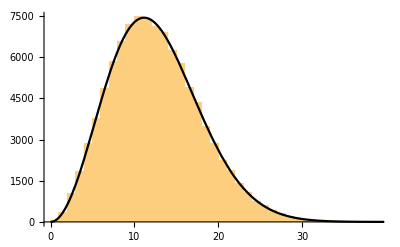

```mathematica
VectorList3=Sqrt@#&/@Total/@(#^2&/@VectorList2);
Show[Histogram[VectorList3,{1}],Plot[100000*PDF[MaxwellDistribution[σ],x],{x,0,50},PlotStyle->Black]]
```

曲线与直方图重合得非常好。故可认为Maxwell分布得到验证。

#### (10).

(a).

∑_(a=1)^∞ C e^(-(a ω)/(k T))=N,∑_(a=1)^∞ a ω C e^(-(a ω)/(k T))=U
Ū=U/N=(∑_(a=1)^∞ a ω C e^(-(a ω)/(k T)))/(∑_(a=1)^∞ C e^(-(a ω)/(k T)))

```mathematica
Simplify[Sum[a ω C E^(-(a ω)/(k T)),{a,1,Infinity}]/Sum[C E^(-(a ω)/(k T)),{a,1,Infinity}]]
```

(ⅇ^(ω/(k T)) ω)/(-1+ⅇ^(ω/(k T)))

故平均能量为(ⅇ^(ω/(k T)) ω)/(-1+ⅇ^(ω/(k T))).

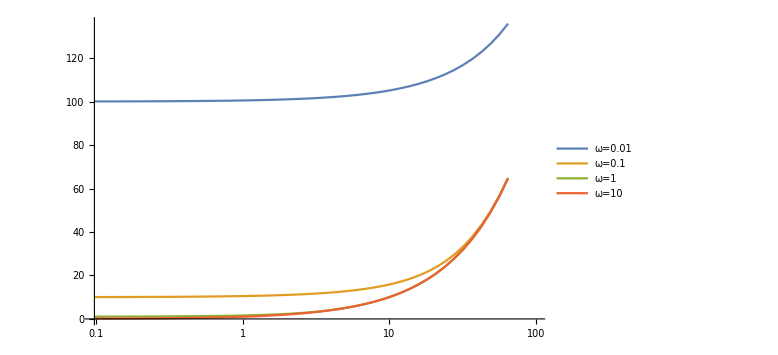

```mathematica
LogLinearPlot[Evaluate[(ⅇ^(ω/(k T)) ω)/(-1+ⅇ^(ω/(k T)))/.1/(k T)->{0.01,0.1,1,10}],{ω,0,100},PlotLegends->Evaluate[StringJoin["ω=",ToString[#]]&/@{0.01,0.1,1,10}],ImageSize->Large]
```

(原图还是见电子文档，颜色打出来不明晰）

{(ⅇ^(0.01 ω) ω)/(-1+ⅇ^(0.01 ω)),(ⅇ^(0.1 ω) ω)/(-1+ⅇ^(0.1 ω)),(ⅇ^ω ω)/(-1+ⅇ^ω),(ⅇ^(10 ω) ω)/(-1+ⅇ^(10 ω))}

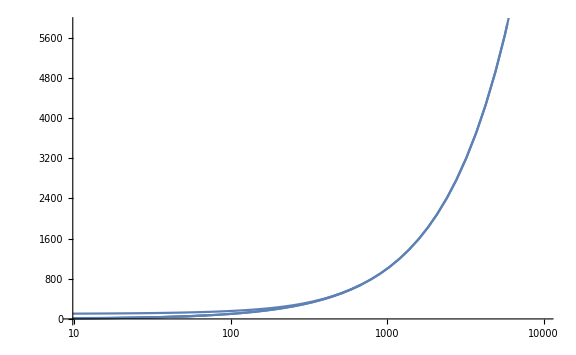

```mathematica
functionlist=(ⅇ^(ω/(k T)) ω)/(-1+ⅇ^(ω/(k T)))/.1/(k T)->#&/@{0.01,0.1,1,10}
Show@@(LogLinearPlot[#,{ω,0,10000},PlotLegends->Automatic,ImageSize->Large]&/@functionlist)
```

(c).

从图中可以看到，频率越高，热容越大（即平均能量随温度升高而升高的幅度越不明显），而温度对热容的影响，

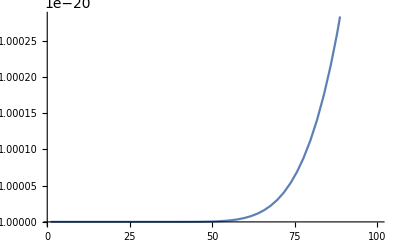

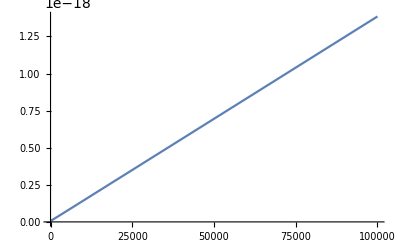

```mathematica
Plot[(ⅇ^(ω/(k T)) ω)/(-1+ⅇ^(ω/(k T)))/.{k->1.38*10^-23,ω->1*10^-20},{T,1,100}]
Plot[(ⅇ^(ω/(k T)) ω)/(-1+ⅇ^(ω/(k T)))/.{k->1.38*10^-23,ω->1*10^-20},{T,1,100000}]
```

可以看到，温度升高会使热容降低。而温度足够高时热容趋近于一个常数。